```mathematica
LogmaxdabsMdk
LogvabsmpmaxdabsMdk
pmaxdabsMdk
pmaxdabsMdk1
```

{{Log[16],3.80877},{Log[24],4.26654},{Log[32],4.58888},{Log[48],5.04109},{Log[64],5.33889}}

{{Log[16],-1.11263},{Log[24],-1.3021},{Log[32],-1.43688},{Log[48],-1.64649},{Log[64],-1.80375}}

{{16,0.22313},{24,0.22249},{32,0.22221},{48,0.22195},{64,0.22183}}

{{24,0.22249},{32,0.22221},{48,0.22195},{64,0.22183}}

```mathematica
ν=1/1.6051220837004385;
k0=0.221671;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=d0+c0*x^(-ex0)
model3=d0+c0*x^(-1/ν)
model4=k0+c0*x^(-ex0)

nlf1=NonlinearModelFit[LogvabsmpmaxdabsMdk,model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxdabsMdk1,model2,{d0,c0,ex0},x];

nlf2[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[pmaxdabsMdk1,model3,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]


nlf4=NonlinearModelFit[pmaxdabsMdk1,model4,{ex0,c0},x];

nlf4[{"BestFit","ParameterTable"}]
```

d0+c0 x^-ex0

d0+c0/x^1.60512

0.221671+c0 x^-ex0

{0.276744-0.497841 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | 0.276744 | 0.0345842 | 8.00204 | 0.00407358
b0 | 0.497841 | 0.00981484 | 50.7233 | 0.0000168749}

{0.221545+0.0458316/x^1.2212, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221545 | 8.41127×10^-7 | 263390. | 2.41702×10^-6
c0 | 0.0458316 | 0.000238353 | 192.284 | 0.0033108
ex0 | 1.2212 | 0.00189262 | 645.244 | 0.000986633}

{0.221671+0.136026/x^1.60512, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221671 | 0.0000172826 | 12826.3 | 6.07851×10^-9
c0 | 0.136026 | 0.00456195 | 29.8175 | 0.00112286}

{0.221671+0.125511/x^1.58072, | Estimate | Standard Error | t-Statistic | P-Value
ex0 | 1.58072 | 0.0648554 | 24.373 | 0.00167914
c0 | 0.125511 | 0.0271828 | 4.61729 | 0.0438439}

```mathematica
val=nlf4["ParameterTableEntries"][[1]][[1]]
```

1.58072

-1.5771

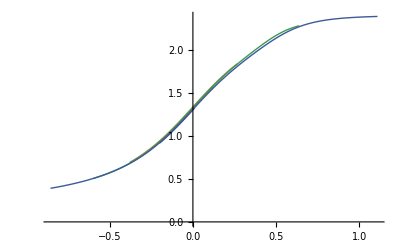

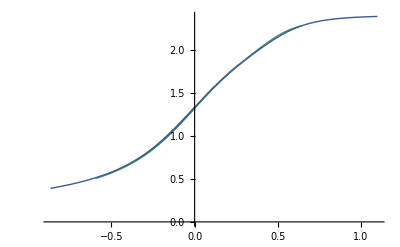

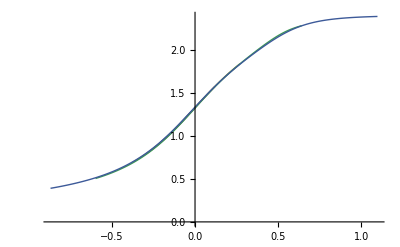

```mathematica
b0=1/ν;
k01=nlf2["ParameterTableEntries"][[1]][[1]];
k02=nlf3["ParameterTableEntries"][[1]][[1]];
k03=k0;
ex01=-nlf2["ParameterTableEntries"][[3]][[1]];
ex02=-1/ν;
ex03=-nlf4["ParameterTableEntries"][[1]][[1]];
a=-nlf1["ParameterTableEntries"][[2]][[1]];
c01=nlf2["ParameterTableEntries"][[2]][[1]];
c02=nlf3["ParameterTableEntries"][[2]][[1]];
c03=nlf4["ParameterTableEntries"][[2]][[1]];


Do[

(*absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

absMs1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs3[l]=Table[{(absM[l][[All,1]][[i]]-(k03+c03*l^(ex03)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

,{l,{16,24,32,48,64}}]
(*ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]*)
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True]
ListPlot[{absMs3[16],absMs3[24],absMs3[32],absMs3[48],absMs3[64]},Joined->True]
```

```mathematica
l1=24;
l2=64;

Do[
input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input3[l]=Table[{(absM[l][[All,1]][[i]]-(k03+c03*l^(ex03))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];
,{l,{l1,l2}}]

aux=1000;
For[z=1.5,z<1.7,z+=0.005,
ClearAll[i];

Do[
dat[l]=Table[{input1[l][[All,1]][[i]]*(l)^z,input1[l][[All,2]][[i]]},{i,1,Length[input1[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=NIntegrate[Abs[i[l1][x]-i[l2][x]],{x,min,max}]/(max-min);
(*Print[val]*)

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.0115884

1.64 = zf

```mathematica
(*Old Method*)
ClearAll[d0,a,z]
l1=24;
l2=32;
l3=48;
l4=64;
sum={};

Do[

input3[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]},{i,1,Length[absM[l]]}]
,{l,{l1,l2,l3,l4}}]

aux=1000;
For[d0=0.21,d0<0.23,d0+=0.001,
For[a=-2,a<0,a+=0.4,
For[z=0,z<2,z+=0.4,


Do[
dat[l]=Table[{(input3[l][[All,1]][[i]]-d0)*(l)^z,input3[l][[All,2]][[i]]}*(l)^a,{i,1,Length[input3[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

(*Print[min,"  ",max]*)

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf=z;
af=a;
d0f=d0;
]
]
]
]
aux
"= zf"zf
"= af" af
"= d0f" d0f
-54.129437674906676
0
-2 "= af"
0.21 "= d0f"
```